```mathematica
Clear["Global`*"]
SetDirectory@NotebookDirectory[];
```

```mathematica
data=Import["bin/logistic.csv"];
```

```mathematica
ListPlot[data,ImageSize->Full]
```

-Graphics-

```mathematica
data=MapThread[
Sort@*Transpose@*List,
{Import["bin/standard_x.csv"],Import["bin/standard_p.csv"]}
];
data=data//Sort;
```

```mathematica
Length@data
```

2401

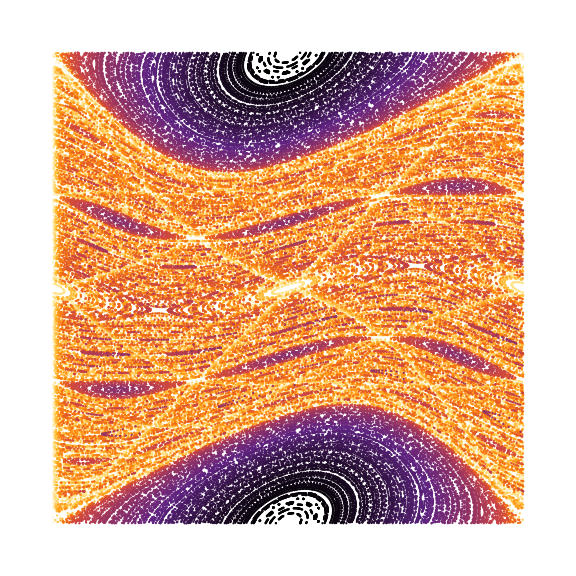

```mathematica
pltStyle=ColorData[{"SunsetColors","Reverse"}]/@Range[0,1,1/(Length@data-1)];
ListPlot[data,ImageSize->Large, Frame->False,Axes->False,AspectRatio->1,PlotStyle->pltStyle]
```